```mathematica
f = -x^3;
g = 2y^3;
```

```mathematica
f=-x^2;
g=2x^2;
```

```mathematica
Solve[16a==D[f, x,x,x]+D[f,x,y,y]+D[g,x,x,y]+D[g,y,y,y]+1/ω(D[f,x,y]*(D[f,x,x]+D[f,y,y])-D[g,x,y]*(D[g,x,x]+D[g,y,y])-D[f,x,x]*D[g,x,x]+D[f,y,y]*D[g,y,y]), a]/.ω->-1
```

{{a→-1/2}}

NDSolve::ndsz: At t == 0.220399, step size is effectively zero; singularity or stiff system suspected.

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

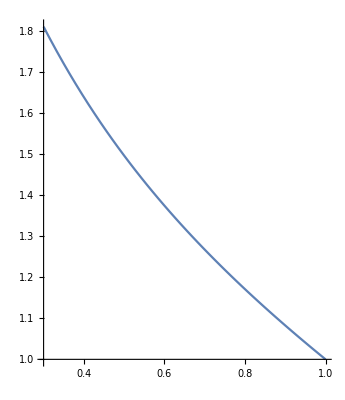

```mathematica
s=NDSolve[{x'[t]==μ*x[t]-3y[t]-x[t]^3,y'[t]== 3x[t]+μ*y[t]+2y[t]^3, x[0]==y[0]==1}/.μ->-1,{x,y},{t,0,10}]

ParametricPlot[Evaluate[{x[t],y[t]}/. s],{t,0,0.139}]
```

```mathematica
(*1 a > 0 subcritical*)
μ = .;
f[x_,y_] = μ*x-3y-x^3;
g[x_,y_] = 3x+μ*y-2y^3;

μ=-1
StreamPlot[{f[x,y],g[x,y]}/.μ->-1,{x,-3,3},{y,-3,3}]
minx = -3; 
maxx = 3;
miny = -3; 
maxy = 3;
sol[x0_ , y0_] := NDSolve[{x'[t] ==μ*x[t]-3*y[t]-x[t]^3, y'[t]==3*x[t]+μ*y[t]-2*y[t]^3 , x[0] ==x0 , y[0] ==y0}, {x,y} , {t, 0, 10}]
initialCondition = Join[Table[{0,y},{y , miny , maxy , 0.1}] ,Table[{minx,y},{y , miny , maxy , 0.1}] , Table[{maxx,y},{y , miny , maxy, 0.1}] , Table[{x,miny},{x , minx , maxx , 0.1}] , Table[{x,maxy},{x , minx , maxx, 0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialCondition[[i,1]] , initialCondition[[i,2]]]], {t,0,10}, PlotRange->{{minx, maxx}, {miny,maxy}}] ,{i,Length[initialCondition]} ]]
```

0

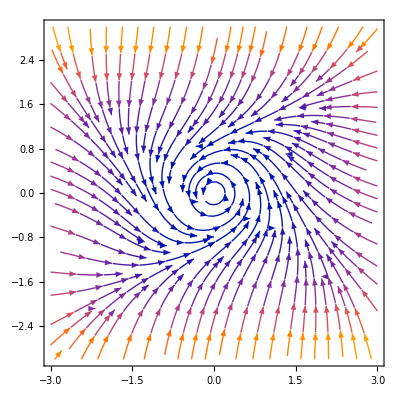

-Graphics-

```mathematica
μ=0
StreamPlot[{f[x,y],g[x,y]}/.μ->0,{x,-3,3},{y,-3,3}]
minx = -3; 
maxx = 3;
miny = -3; 
maxy = 3;
sol[x0_ , y0_] := NDSolve[{x'[t] ==μ*x[t]-3*y[t]-x[t]^3, y'[t]==3*x[t]+μ*y[t]-2*y[t]^3 , x[0] ==x0 , y[0] ==y0}, {x,y} , {t, 0, 10}]
initialCondition = Join[Table[{minx,y},{y , miny , maxy , 0.1}] , Table[{maxx,y},{y , miny , maxy, 0.1}] ,Table[{x,miny},{x , minx , maxx , 0.1}] , Table[{x,maxy},{x , minx , maxx, 0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialCondition[[i,1]] , initialCondition[[i,2]]]], {t,0,10}, PlotRange->{{minx, maxx}, {miny,maxy}}] ,{i,Length[initialCondition]} ]]
```

-1

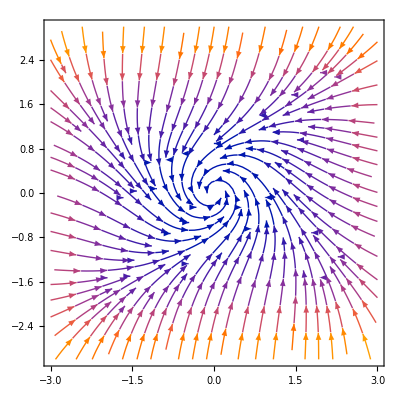

-Graphics-

0

-Graphics-

-Graphics-

1

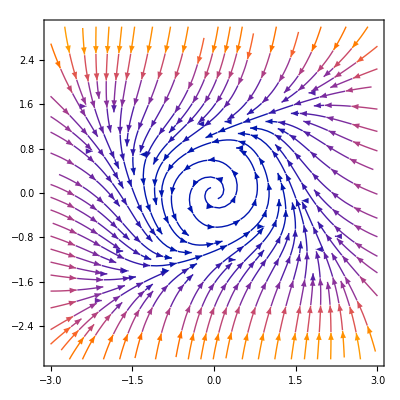

-Graphics-

```mathematica
μ=1
StreamPlot[{f[x,y],g[x,y]}/.μ->1,{x,-3,3},{y,-3,3}]
minx = -3; 
maxx = 3;
miny = -3; 
maxy = 3;
sol[x0_ , y0_] := NDSolve[{x'[t] ==μ*x[t]-3*y[t]-x[t]^3, y'[t]==3*x[t]+μ*y[t]-2*y[t]^3 , x[0] ==x0 , y[0] ==y0}, {x,y} , {t, 0, 10}]
initialCondition = Join[Table[{0,y},{y , miny , maxy , 0.1}] ,Table[{minx,y},{y , miny , maxy , 0.1}] , Table[{maxx,y},{y , miny , maxy, 0.1}] , Table[{x,miny},{x , minx , maxx , 0.1}] , Table[{x,maxy},{x , minx , maxx, 0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialCondition[[i,1]] , initialCondition[[i,2]]]], {t,0,10}, PlotRange->{{minx, maxx}, {miny,maxy}}] ,{i,Length[initialCondition]} ]]
```

-1

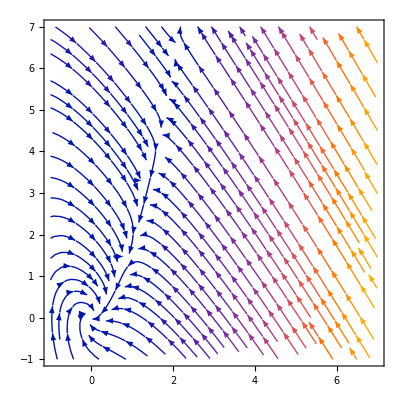

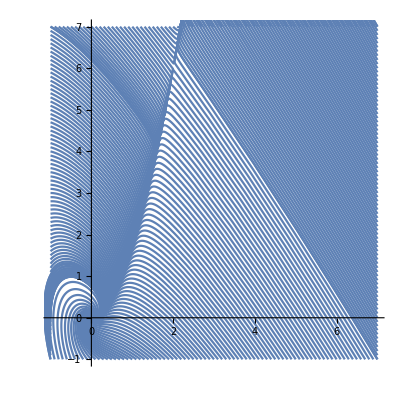

```mathematica
(*2 a < 0 supercritical*)
Clear["Global`*"]
μ = .;
f[x_,y_] = μ*x+y-x^2;
g[x_,y_] = -x+μ*y+2x^2;

μ=-1
Solve[f[x,y]==0&&g[x,y]==0, {x,y}];
StreamPlot[{f[x,y],g[x,y]},{x,-1,7},{y,-1,7}]
minx = -1; 
maxx = 7;
miny = -1; 
maxy = 7;
sol[x0_ , y0_] := NDSolve[{x'[t] ==μ*x[t]+y[t]-x[t]^2, y'[t]==-x[t]+μ*y[t]+2*x[t]^2 , x[0] ==x0 , y[0] ==y0}, {x,y} , {t, 0, 10}]
initialCondition = Join[Table[{minx,y},{y , miny , maxy , 0.1}] , Table[{maxx,y},{y , miny , maxy, 0.1}] , Table[{x,miny},{x , minx , maxx , 0.1}] , Table[{x,maxy},{x , minx , maxx, 0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialCondition[[i,1]] , initialCondition[[i,2]]]], {t,0,10}, PlotRange->{{minx, maxx}, {miny,maxy}}] ,{i,Length[initialCondition]} ]]
```

```mathematica
μ=0
Solve[f[x,y]==0&&g[x,y]==0, {x,y}];
StreamPlot[{f[x,y],g[x,y]},{x,-1, 1},{y,-1,1}]
minx = -1; 
maxx = 1;
miny = -1; 
maxy = 1;
sol[x0_ , y0_] := NDSolve[{x'[t] ==μ*x[t]+y[t]-x[t]^2, y'[t]==-x[t]+μ*y[t]+2*x[t]^2 , x[0] ==x0 , y[0] ==y0}, {x,y} , {t, 0, 10}]
initialCondition = Join[Table[{minx,y},{y , miny , maxy , 0.05}] ,Table[{x,0},{x , 0 , 0.2, 0.05}] ,Table[{maxx,y},{y , miny , maxy, 0.05}] , Table[{x,miny},{x , minx , maxx , 0.05}] , Table[{x,maxy},{x , minx , maxx, 0.05}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialCondition[[i,1]] , initialCondition[[i,2]]]], {t,0,10}, PlotRange->{{minx, maxx}, {miny,maxy}}] ,{i,Length[initialCondition]} ]]
```

0

-Graphics-

-Graphics-

```mathematica
μ=1
Solve[f[x,y]==0&&g[x,y]==0, {x,y}];
StreamPlot[{f[x,y],g[x,y]},{x,-1,1},{y,-1,1}]
minx = -1; 
maxx = 1;
miny = -1; 
maxy = 1;
sol[x0_ , y0_] := NDSolve[{x'[t] ==μ*x[t]+y[t]-x[t]^2, y'[t]==-x[t]+μ*y[t]+2*x[t]^2 , x[0] ==x0 , y[0] ==y0}, {x,y} , {t, 0, 10}]
initialCondition = Join[Table[{0,y},{y , miny , maxy , 0.01}] , Table[{x,0},{x , minx , maxx , 0.01}], Table[{1,y},{y , 0 , -1 , -0.01}] ];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialCondition[[i,1]] , initialCondition[[i,2]]]], {t,0,10}, PlotRange->{{minx, maxx}, {miny,maxy}}] ,{i,Length[initialCondition]} ]]
```

1

-Graphics-

-Graphics-